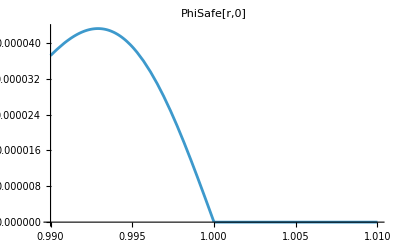

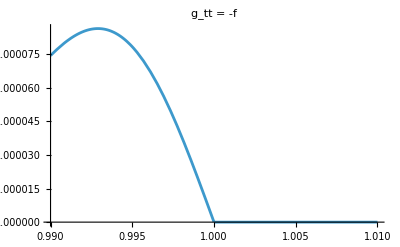

General::munfl: Exp[-9801.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9799.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Central Energy Density: 0

General::munfl: Exp[-9801.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9799.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NEC at (0,0): 0

NEC at (1,0): -49.9897

General::munfl: Exp[-9801.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9799.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

WEC at (0,0): 0

WEC at (1,0): 2.98415×10^-6

General::munfl: Exp[-9801.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9799.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DEC at (0,0): True

DEC at (1,0): True

Total Exotic Energy: 0.

General::munfl: Exp[-9798.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9797.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9798.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9797.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9798.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9797.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9801.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9799.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Stress-energy tensor at (0,0):

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

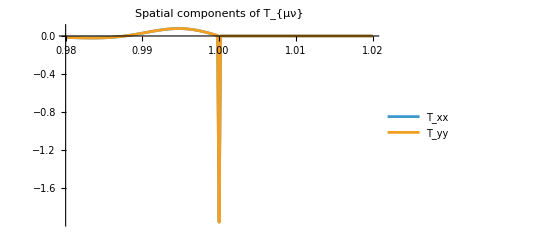

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00023}. NIntegrate obtained 0.0000510757 and 1.12907×10^-7 for the integral and error estimates.

0.0000510757

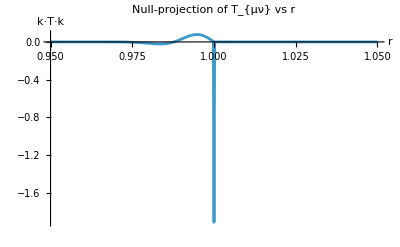

```mathematica
(* ===PARAMETERS===*)R0=1.0;
(*A=0.00001*) A = 0.01;
(*w=0.0001*)w=0.01;
ϵ=0.01;

(* ===SAFE POTENTIAL===*)
ϕSafe[x_,y_]:=Module[{r},r=Max[Sqrt[x^2+y^2],ϵ];
Max[-A*(1-R0/r)*Exp[-((r-R0)^2/w^2)],10^-15]];

(* ===METRIC AND INVERSE METRIC===*)
metricVal[x_,y_]:=Module[{f},f=Exp[2 ϕSafe[x,y]];
{{-f,0,0},{0,1/f,0},{0,0,1/f}}];

invMetricVal[x_,y_]:=Module[{f},f=Exp[-2 ϕSafe[x,y]];
{{-f,0,0},{0,f,0},{0,0,f}}];
Plot[ϕSafe[r,0],{r,0.99,1.01},PlotLabel->"PhiSafe[r,0]"]
Plot[Exp[2 ϕSafe[r,0]],{r,0.99,1.01},PlotLabel->"g_tt = -f"]
(* ===NUMERICAL DERIVATIVE===*)
deriv[f_,x0_,y0_,var_,h_:10^-4]:=If[var==1,(f[x0+h,y0]-f[x0-h,y0])/(2 h),(f[x0,y0+h]-f[x0,y0-h])/(2 h)];

(* ===CHRISTOFFEL SYMBOL===*)
Christoffel[x_,y_,μ_,ν_,ρ_]:=Module[{ig=invMetricVal[x,y]},Sum[1/2 ig[[μ,σ]]*(deriv[Function[{a,b},metricVal[a,b][[σ,ν]]],x,y,ρ]+deriv[Function[{a,b},metricVal[a,b][[σ,ρ]]],x,y,ν]-deriv[Function[{a,b},metricVal[a,b][[ν,ρ]]],x,y,σ]),{σ,1,3}]]

(* ===RICCI TENSOR===*)
Ricci[x_,y_,mu_,nu_]:=Module[{sum=0},sum=Sum[deriv[Function[{a,b},Christoffel[a,b,sigma,mu,sigma]],x,y,nu]-deriv[Function[{a,b},Christoffel[a,b,sigma,mu,nu]],x,y,sigma]+Sum[Christoffel[x,y,sigma,kappa,nu]*Christoffel[x,y,kappa,mu,sigma]-Christoffel[x,y,sigma,kappa,sigma]*Christoffel[x,y,kappa,mu,nu],{kappa,1,3}],{sigma,1,3}];
sum];

(* ===RADIUS-DEPENDENT NULL VECTOR===*)kNull[r_]:={1,Exp[2 ϕSafe[r,0]],0};   (*always null for our metric*)
(* ===STRESS ENERGY TENSOR===*)
stressEnergy[x_,y_]:=Module[{g,ig,R,RicciScalar},g=metricVal[x,y];
ig=invMetricVal[x,y];
R=Table[Ricci[x,y,mu,nu],{mu,1,3},{nu,1,3}];
RicciScalar=Tr[ig.R];
Table[(1/(8 Pi))*(R[[mu,nu]]-1/2 g[[mu,nu]]*RicciScalar),{mu,1,3},{nu,1,3}]];

(* ===SAFE DIVISION ENERGY DENSITY===*)
safeDivide[a_,b_]:=If[Abs[b]<10^-14,0,a/b];

energyDensity[x_,y_]:=Module[{g,ig,R},g=metricVal[x,y];ig=invMetricVal[x,y];
R=Table[Ricci[x,y,mu,nu],{mu,1,3},{nu,1,3}];
safeDivide[-(R[[1,1]]-1/2 g[[1,1]] Tr[ig.R]),g[[1,1]]]];

(* ===NEC===*)
nullVec={1,1,0};
NEC[x_,y_]:=Module[{g,ig,R,T},g=metricVal[x,y];ig=invMetricVal[x,y];
R=Table[Ricci[x,y,mu,nu],{mu,1,3},{nu,1,3}];
T=Table[R[[mu,nu]]-1/2 g[[mu,nu]] Tr[ig.R],{mu,1,3},{nu,1,3}];
Chop[nullVec.T.nullVec]];

(* ===WEC===*)
timelikeVec={1,0,0};
WEC[x_,y_]:=Module[{T},T=stressEnergy[x,y];
Chop[timelikeVec.T.timelikeVec]];

(* ===DEC===*)
DEC[x_,y_]:=Module[{T,flowVec,norm,g},T=stressEnergy[x,y];
g=metricVal[x,y];flowVec=T.timelikeVec;
norm=flowVec.g.flowVec;
If[WEC[x,y]>=0&&norm<=0,True,False]];

(* ===INTEGRAND FOR EXOTIC ENERGY===*)
polarIntegrand[r_?NumericQ]:=Module[{g},If[r<ϵ,0,g=metricVal[r,0];
r*energyDensity[r,0]*Sqrt[Abs[-Det[g]]]]];

(* ===TOTAL EXOTIC ENERGY===*)
totalExoticEnergy:=NIntegrate[polarIntegrand[r],{r,ϵ,5},Method->{"GlobalAdaptive","SingularityHandler"->"DoubleExponential"},AccuracyGoal->4,PrecisionGoal->4];

(* ===OUTPUT===*)
Print["Central Energy Density: ",energyDensity[ϵ,0.0]];
Print["NEC at (0,0): ",NEC[ϵ,0.0]];
Print["NEC at (1,0): ",NEC[1.0,0.0]];
Print["WEC at (0,0): ",WEC[ϵ,0.0]];
Print["WEC at (1,0): ",WEC[1.0,0.0]];
Print["DEC at (0,0): ",DEC[ϵ,0.0]];
Print["DEC at (1,0): ",DEC[1.0,0.0]];
Print["Total Exotic Energy: ",totalExoticEnergy];

(* ===VISUALIZATION===*)
Plot[energyDensity[r,0],{r,ϵ,5},PlotLabel->"Energy Density Profile",AxesLabel->{"r","ρ(r)"}];

Plot[WEC[r,0],{r,ϵ,5},PlotLabel->"Weak Energy Condition (WEC)",AxesLabel->{"r","T_{00}"}];

Plot[If[DEC[r,0],1,0],{r,ϵ,5},PlotLabel->"Dominant Energy Condition (1=True, 0=False)",AxesLabel->{"r","DEC satisfied"}];

(*Compute the tensor*)tensor=stressEnergy[ϵ,0.0];

(*Display it*)
Print["\nStress-energy tensor at (0,0):"];
MatrixForm[tensor]

(* ===GENERALIZED NEC TEST FOR ALL NULL VECTORS===*)(*Parameterize null vectors in 2D*)nullVector[theta_]:={1,Sin[theta],Cos[theta]};

(*Verify null condition:k^μ k_μ=0*)
nullCondition[x_,y_,theta_]:=Module[{g,k},g=metricVal[x,y];
k=nullVector[theta];
Chop[k.g.k]==0];

(*NEC for arbitrary null vectors*)
generalNEC[x_,y_,theta_]:=Module[{g,ig,R,T,k},g=metricVal[x,y];ig=invMetricVal[x,y];
R=Table[Ricci[x,y,mu,nu],{mu,1,3},{nu,1,3}];
T=Table[(1/(8 Pi))*(R[[mu,nu]]-1/2 g[[mu,nu]] Tr[ig.R]),{mu,1,3},{nu,1,3}];
k=nullVector[theta];
Chop[k.T.k]];

(*Test NEC for multiple angles at a given (x,y)*)
testNECAtPoint[x_,y_,angles_:Range[0,2 Pi,Pi/8]]:=Table[{theta,generalNEC[x,y,theta]},{theta,angles}];

(*Visualize NEC violation*)
plotNECViolation[x_,y_]:=ListPlot[testNECAtPoint[x,y],PlotLabel->StringForm["NEC for null vectors at (``,``)",x,y],AxesLabel->{"θ (rad)","T_{\μ\ν}k^\μk^\ν"},PlotRange->All,Joined->True,Mesh->All];

TComp[μ_,ν_][r_]:=stressEnergy[r,0][[μ,ν]];

Plot[Evaluate@{TComp[2,2][r],TComp[3,3][r]},(*spatial stresses*){r,0.98,1.02},PlotRange->All,PlotLegends->{"T_xx","T_yy"},PlotLabel->"Spatial components of T_{μν}"]

nullVec={1,1,0};  (*or {1,1/Sqrt[2],1/Sqrt[2]} for normalized*)

exoticIntegrand[r_]:=Module[{g=metricVal[r,0],ig=invMetricVal[r,0],R,T,k},R=Table[Ricci[r,0,μ,ν],{μ,1,3},{ν,1,3}];
T=Table[(1/(8 Pi)) (R[[μ,ν]]-1/2 g[[μ,ν]] Tr[ig.R]),{μ,1,3},{ν,1,3}];
k=kNull[r];(*  ←here*)r*(k.T.k)*Sqrt[Abs[-Det[g]]]]

NIntegrate[exoticIntegrand[r],{r,0.98,1.02}]

NECdensity[r_]:=Module[{g=metricVal[r,0],ig=invMetricVal[r,0],R,T},R=Table[Ricci[r,0,μ,ν],{μ,1,3},{ν,1,3}];
T=Table[(1/(8 Pi)) (R[[μ,ν]]-1/2 g[[μ,ν]] Tr[ig.R]),{μ,1,3},{ν,1,3}];
kNull[r].T.kNull[r]]

Plot[NECdensity[r],{r,0.95,1.05},PlotRange->All,AxesLabel->{"r","k·T·k"},PlotLabel->"Null-projection of T_{μν} vs r"]
```